```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_Tiingo_ETH/";
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
F2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

Make density out of cdf

-Graphics-

```mathematica
f2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[fNIG[x-z,α,β,μ1,δ1] fNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{5.30705,0.547637}

```mathematica
Timing[f2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{0.017027,0.3921}

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},n=Length[s];If[Length[x]==0,N[Length[Select[s,#1≤x&]]/(n+1)],Table[N[Length[Select[s,#1≤x⟦k⟧&]]/(n+1)],{k,1,Length[x]}]]]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | eth Price | log return future | log return eth
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 2784.74 | 0.0212907 | 0.068794
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 2599.61 | -0.0904653 | -0.269777
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 3404.63 | -0.0196938 | 0.00767698
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 3378.6 | -0.131645 | -0.18102
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 4049.04 | 0.03685 | 0.103942
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 3649.31 | -0.119603 | -0.11274
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 4084.82 | -0.042369 | 0.0033428
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 4071.19 | 0.018947 | 0.0196738
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 3991.88 | -0.0359909 | 0.127305)

```mathematica
data[[1,7]]
```

log return eth

```mathematica
data[[1,6]]
```

log return future

```mathematica
tmp=Import[NotebookDirectory[] <> "data_eth/" <> ToString[kk] <> "_parameters.csv"]
```

(2021-05-20
0.866957
-0.389032
0.473983)

```mathematica
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
```

```mathematica
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

Attempt to determine LL from simulated data turns out to be very noisy

```mathematica
tmp=Import[NotebookDirectory[] <> "data_eth/" <> ToString[kk] <> "_simulation.csv"];
```

```mathematica
tmp[[1;;10]]
```

(0.131997 | 0.0538589
0.00245995 | 0.00239995
0.583708 | 0.468891
0.641947 | 0.453951
0.921462 | 0.901622
0.823644 | 0.967501
0.907762 | 0.773125
0.778304 | 0.590628
0.525589 | 0.661247
0.99164 | 0.99506)

```mathematica
Dimensions[tmp]
```

{50000,2}

```mathematica
uv=tmp;
skd=SmoothKernelDistribution[uv];
```

-Graphics-

copula density

```mathematica
c2NIG[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{x,y},
x=NIGInv[u,α,β];
y=NIGInv[v,α,β];
f2NIG[x,y,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ] / (NIGPDF[x,α,β] NIGPDF[y,α,β])
]
```

```mathematica
Timing[c2NIG[0.5,0.1,5,0,0.2]]
```

{0.087086,0.998887}

-Graphics-

-Graphics-

```mathematica
c2NIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.860228,1.09924,0.554866,32.0436,1.17214}

```mathematica
PDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{0.930606,3.11928,0.605355,2.9165,1.43127}

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
CNIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.658281,0.00263523,0.17986,0.00479535,0.807546}

```mathematica
CDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{0.657139,0.00778227,0.179331,0.00552459,0.804776}

```mathematica
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)]
```

119.803

```mathematica
%/Length[data]
```

0.398016

```mathematica
Timing[Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)]]
```

{16.4319,134.265}

```mathematica
%/Length[data]
```

{0.0545912,0.446064}

```mathematica
tLL={};
mLL={};
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
tmp=Import[NotebookDirectory[] <> "data_eth/" <> ToString[kk] <> "_parameters.csv"];
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
ll=Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLL, ll];
AppendTo[mLL,mll];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.82739}. NIntegrate obtained 0.00305824 and 5.17457×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-5.32161}. NIntegrate obtained 0.00332998 and 4.81073×10^-9 for the integral and error estimates.

```mathematica
(*tLLnew={};
mLLnew={};
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
uv=Import[NotebookDirectory[] <> "data_xrp/" <> ToString[kk] <> "_simulation.csv"];
skd=SmoothKernelDistribution[uv];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLnew, ll];
AppendTo[mLLnew,mll];
]*)
```

```mathematica
tLL
```

{134.265,148.182,153.359,166.847,167.108,174.116,173.541,153.463,154.87,155.179,153.777,167.124,153.712,154.983,163.298,172.786,190.591,179.387,190.963,168.214,180.861,183.684,190.058,190.352,169.407,170.447,183.346,186.838,175.492,175.734,172.178,171.679,169.835,169.894,170.994,179.614,176.386,174.607,184.047,184.136,164.875,191.457,199.332,192.771,189.371,184.641,187.212,187.536,178.65,191.278,192.643,183.185,187.358,179.687,181.325,184.482,182.683,178.723,183.734,183.419,176.384,165.507,173.166,164.512,168.102,184.132,185.861,177.385,174.51,180.678,181.23,174.175,185.319,183.902,184.535,182.915,175.325,174.945,178.492,181.449,182.425,176.581,174.179,173.659,178.086,187.224,194.17,191.07,191.85,196.79,205.719,204.658,208.248,210.46,200.377,202.729,203.991,206.691,207.967,210.62,210.519,207.423,210.35,208.59,208.19,200.687,193.232,197.402,191.725,197.232,175.052,166.168}

```mathematica
mLL
```

{0.446064,0.492299,0.509499,0.55431,0.555177,0.578459,0.576547,0.509843,0.514519,0.515543,0.510888,0.555231,0.510672,0.514893,0.54252,0.574041,0.633193,0.595971,0.634429,0.55885,0.600867,0.610247,0.63142,0.6324,0.562815,0.566269,0.609122,0.620725,0.583029,0.583832,0.57202,0.570361,0.564234,0.564433,0.568087,0.596724,0.586001,0.58009,0.611451,0.611746,0.547759,0.636068,0.662234,0.640437,0.629138,0.613427,0.621968,0.623043,0.59352,0.635476,0.640009,0.608587,0.622453,0.596967,0.602409,0.612896,0.60692,0.593764,0.610413,0.609366,0.585993,0.549857,0.575304,0.54655,0.558478,0.611734,0.617479,0.589318,0.579767,0.60026,0.602094,0.578655,0.615678,0.610972,0.613073,0.607692,0.582474,0.581211,0.592998,0.602822,0.606065,0.586648,0.578669,0.57694,0.591649,0.622005,0.645082,0.634784,0.637377,0.653788,0.683451,0.679928,0.691854,0.699203,0.665703,0.673517,0.677712,0.686683,0.690919,0.699734,0.699398,0.689112,0.698836,0.69299,0.691661,0.666734,0.641968,0.655821,0.636959,0.655256,0.581567,0.552052}

```mathematica
Export[NotebookDirectory[] <> "data_eth/LL_NIG_eth.csv", Prepend[{Range[0,111],tLL, mLL}ᵀ, {"", "LL", "mean LL"}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data_eth/LL_NIG_eth.csv

```mathematica
(*Export[NotebookDirectory[] <> "data_xrp/LL_NIG_new.csv", Prepend[{Range[0,87],tLLnew, mLLnew}ᵀ, {"", "LL", "mean LL"}]]*)
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data/LL_NIG_new.csv

Gaussian copula

```mathematica
LLg[x_]:=Log[PDF[BinormalDistribution[{0,0}, {1,1}, ρ], x]]-Total[Log[PDF[NormalDistribution[],#]&/@x]]
```

```mathematica
ρ=0.9907220113152815;
ρ=0.9891018086831789;
```

```mathematica
tLLg={};
mLLg={};
For[kk=1, kk<=1, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLg[{InverseCDF[NormalDistribution[],#[[1]]],InverseCDF[NormalDistribution[],#[[2]]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLg, ll];
AppendTo[mLLg,mll];
]
```

```mathematica
tLLg
```

{365.689}

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Z=RandomVariate[NormalDistribution[],{100000,2}];
```

```mathematica
X=Z[[;;,1]];
Y=ρ Z[[;;,1]] + Sqrt[1-ρ^2] Z[[;;,2]];
```

```mathematica
U=hatF[X];
V=hatF[Y];
```

```mathematica
skd=SmoothKernelDistribution[{U,V}ᵀ];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
```

```mathematica
ll
```

382.909

Clayton copula

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

```mathematica
LLc[u_]:=Log[PDF[𝒟, u]]-Total[Log[#&/@u]]
```

```mathematica
c=40;
```

```mathematica
tLLc={};
mLLc={};
For[kk=18, kk<=18, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLc[{#[[1]],#[[2]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLc, ll];
AppendTo[mLLc,mll];
]
```

```mathematica
tLLc
```

{548.926}

```mathematica
mLLc
```

{1.82367}

```mathematica
Quantile[𝒟, {0.5, 0.5}]
```

Quantile[CopulaDistribution[{Clayton,1/40},{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{0.5,0.5}]

-Graphics-

```mathematica
ClaytonCDF[u_,v_]:=(u^-c+v^-c-1)^(-1/c)
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

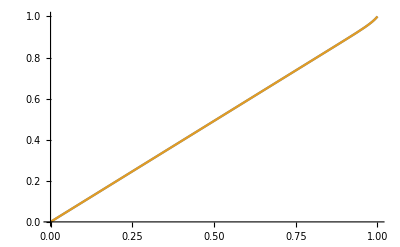

```mathematica
Plot[{CDF[𝒟, {u,u}],ClaytonCDF[u,u]}, {u,0,1}]
```

```mathematica
Simplify[ClaytonCDF[q,q]/q]
```

1/((2/q^40-1)^(1/40) q)

```mathematica
Simplify[CDF[𝒟,{q,q}]/q, Assumptions->0<q<1]
```

1/((2-q^40)^(1/40))

```mathematica
QD[q_?NumericQ]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
QD2[q_?NumericQ]:=
If[0<q≤0.5, ClaytonCDF[q,q]/q,(1-2q+ ClaytonCDF[q,q])/(1-q)]
```

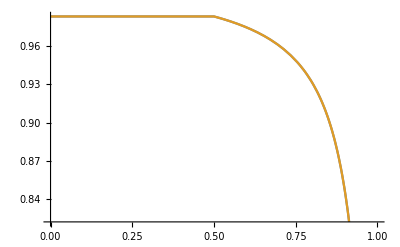

```mathematica
Plot[{QD[q],QD2[q]}, {q,0,1}]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
kk=18;
```

```mathematica
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

```mathematica
Clear[c, QD,𝒟]
```

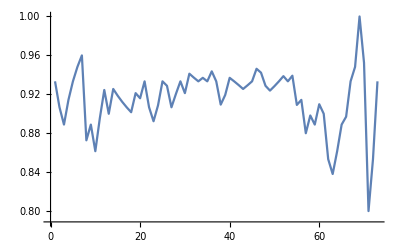

```mathematica
ListPlot[Table[QDemp[q, u, v], {q,0.05,0.95, 0.0125}],Joined->True]
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
QD[q_]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
target=Table[QDemp[q, u, v], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[target, KendallTau[u,v]];
target
```

{0.933333,0.933333,1.,0.933333,0.884563}

```mathematica
f= Table[QD[q], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[f, c/(c+2)]; (* Kendall's tau *)
Sqrt[Total[(target-f)^2]]
```

√((0.933333-20. (2 0.05^-c-1)^(-1/c))^2+(0.933333-10. (2 0.1^-c-1)^(-1/c))^2+(1.-10. ((2 0.9^-c-1)^(-1/c)-0.8))^2+(0.933333-20. ((2 0.95^-c-1)^(-1/c)-0.9))^2+(0.884563-c/(c+2))^2)

```mathematica
NMinimize[{Sqrt[Total[(target-f)^2]], c>0}, c]
```

{0.141561,{c→181.081}}

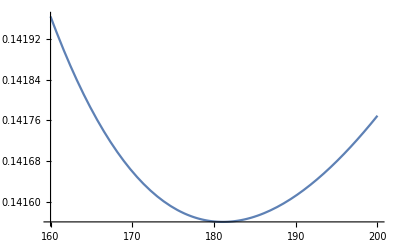

```mathematica
Plot[Sqrt[Total[(target-f)^2]], {c,160,200}]
```